```mathematica
ClearAll["Global`*"];
```

```mathematica
Nmax = 100;
Nexp=10;
```

```mathematica
SetPrecision[rp=1,15];
SetPrecision[l=1,15];
SetPrecision[k=0,15];
SetPrecision[η=0,15];
SetPrecision[m=0,15];
SetPrecision[ξ=0,15];
nover =1;
scalar=0;
M1=M/.Solve[-M+rp^2/l^2==0,M][[1]];
```

```mathematica
F=Simplify[-N[M1]+r^2/l^2];
H=Simplify[1/F];
V=3r^2/(4l^4)-N[M1]/(2l^2)-N[M1]^2/(4r^2)+k^2(1/l^2-N[M1]/r^2);
```

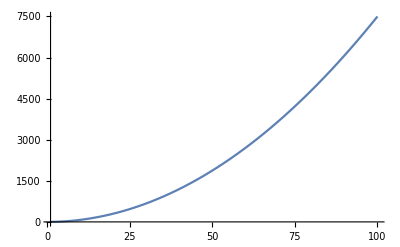

```mathematica
Plot[V,{r,rp,100}]
```

```mathematica
r=1/x;
```

```mathematica
A1=Simplify[F];
B1=Simplify[H];
V1= Simplify[V];
DDV=D[V1,x];
xp=1/rp;
```

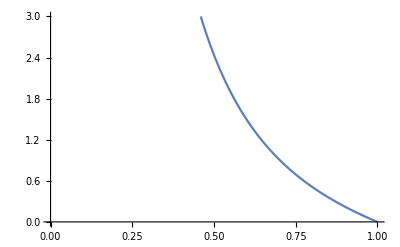

```mathematica
Plot[V1,{x,0,xp},PlotPoints-> {20000},PlotRange-> {0,3}]
```

```mathematica
xp=1/rp;
```

```mathematica
SQRTAB=Simplify[F];
```

```mathematica
S[x_]=Chop[ SetPrecision[-1/(x-xp)Simplify[x^4 SQRTAB],15]];
T[x_]=Chop[SetPrecision[-Simplify[(2x^3 SQRTAB+x^4  D[SQRTAB,x]+2I w x^2)],15]];
U[x_]=Chop[SetPrecision[(x-xp)Simplify[(1/SQRTAB  V1 )],15]];
```

```mathematica
S1[x_]=Chop[SetPrecision[Normal[Series[S[x],{x,xp,Nmax}]],15]];
T1[x_]=Chop[SetPrecision[Normal[Series[T[x],{x,xp,Nmax}]],15]];
U1[x_]= Chop[SetPrecision[Normal[Series[U[x],{x,xp,Nmax}]],15]];
```

```mathematica
s=Chop[Simplify[(Table[1/(i!) D[S1[x],{x,i}],{i,0,Nmax}])/.x->xp]];
t=Simplify[(Table[1/(i!) D[T1[x],{x,i}],{i,0,Nmax}])/.x->xp];
u=Simplify[(Table[1/(i!) D[U1[x],{x,i}],{i,0,Nmax}])/.x->xp];
```

```mathematica
DENOMINADOR=SetPrecision[Table[Simplify[i*(i-1)*s[[1]] + i*t[[1]]],{i,1,Nmax}],15];
```

```mathematica
an={1};
Do[
aproximo = Sum[
                 (  (j-1)*(j-2)*s[[i-j+2]] + (j-1)*t[[i-j+2]] + u[[i-j+2]]  )*an[[j]]
                     ,{j,1,i}];
  an=Append[an,Together[aproximo/(-DENOMINADOR[[i]])]]
,{i,1,Nmax}]
```

```mathematica
wfund[NSoma_]:= 
Module[{zeromaquina,psi, poly, modos0,modos1,modos2},

psi[w_]=Together[Sum[an[[i]]*(-xp)^i,{i,1, NSoma}]];
poly=Numerator[psi[w]];

modos0= w/.SetPrecision[NSolve[poly==0&& -500<Im[w]<0,w],15];

zeromaquina = 10^(-5);
cond1[x_/;Re[x]<=zeromaquina]:=True;
modos1=Select[modos0,cond1];
modos2=Sort[modos1,Im[#1]>Im[#2]&];
{NSoma,modos2}
]
```

```mathematica
TabelaIm = {};
TabelaRe = {};

Do[
wcalculado =  wfund[i];
TabelaIm = Append[TabelaIm,{wcalculado[[1]],Im[wcalculado[[2]][[nover]]]} ];
TabelaRe = Append[TabelaRe,{wcalculado[[1]],Re[wcalculado[[2]][[nover]]]} ];
,{i,4,Nmax}
  ]//Timing
```

Select::normal: Nonatomic expression expected at position 1 in Select[w,cond1].

{173.906,Null}

```mathematica
TabelaRe[[Nmax-3]][[2]] + I TabelaIm[[Nmax-3]][[2]]
```

-2.00012747995963 ⅈ

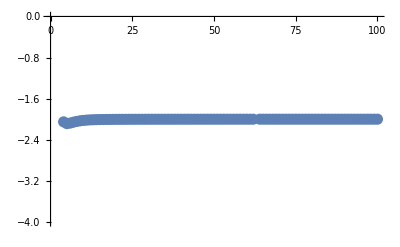

```mathematica
grafIm=ListPlot[TabelaIm,PlotStyle->PointSize[0.02],PlotRange->{-4,0}]
```

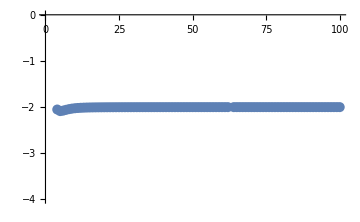

```mathematica
Show[grafIm,ImageSize->Medium]
```

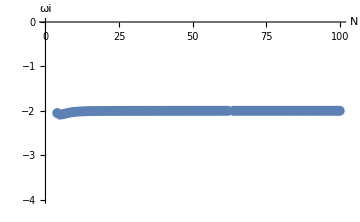

```mathematica
Show[%96,AxesLabel->{HoldForm[N],HoldForm[ωi]},PlotLabel->None,LabelStyle->{18,GrayLevel[0]}]
```

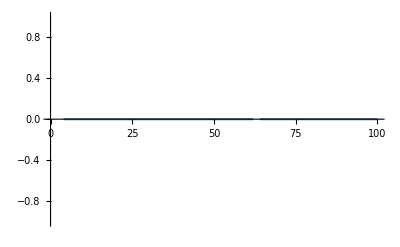

```mathematica
grafRe=ListPlot[TabelaRe,PlotStyle->PointSize[0.02],Joined->True]
```